CSE 477 * Intro to CAGD
Instructor: Dianne Hansford
Homework 4: B-spline Curve Design, ConS, and 3D Printing
Anish Nalla

Big picture: You will create an artistic/fun pretzel-like 2d B-spline curve. This curve will be used to create a CONS (on a Bezier surface). You will make two more copies of the CONS, moving them in 3D space, so that the resulting three 3d curves form a chain, and then you will create a 3d print of this object. Steps for this are described below.


Objectives:
-- experience designing with B-splines
-- more surface design experience
-- improve understanding of 3d geometry
-- understand the concept of Curves on Surfaces (ConS)
-- hands-on experience with 3d printing  

Details:
step 1) Using  one 2d cubic B-spline curve, design an artistic curve with a pretzel-like shape (at least two loops) in the xy-plane.
The B-spline must have the following properties.
-- at least ten polynomial segments,
-- full multiplicity at the ends,
-- start point is equal to the end point (closed but not periodic)
-- at least one interior domain knot must have multiplicity 2
-- at least one interior domain knot must have multiplicity 3
The control points should live in [0,1] x [0,1] in order to live in the domain of a Bezier surface. (If needed, you can use a translation and/or scale to achieve this.)
You may use MM’s B-spline function BSplineCurve[] for display, but you will need your own evaluator to extract (x,y) points (that will be interpreted as (u,v) for the surface).  Your own evaluator will use BSplineBasis[]. (You may use code from the demo nbs.)

Plot your curve in 2D with the control points and polygon, using different colors for the curve and control polygon/points.
Print the knot vector and the number of curve segments next to this plot.
 
step 2) Design an interesting/curvey Bezier patch. The patch must be at least bicubic. (You could use the Coons method.)

step 3) Plot your B-spline curve as a ConS together with the surface. Include the Bezier control net in this plot.

step 4) Plot the ConS without the surface displayed. Use the Tube function to give it thickness. 
Please take some time to set the thickness parameter to a “reasonable” value because this will influence the 3D print quality. (Too thin and the print will not be stable enough; too thick and your design concept is lost.)

step 5) Translate the ConS twice, creating three curves that are chained together and do not intersect.
This will require a bit of “eyeballing it.” You could modify your ParametricPlot3D from step 4 to look like this:
ParametricPlot3D[{surf[....],   surf[...] + {x1, y1, z1}, surf[...] + {x2, y2, z2}} ....]
where the “...” is code you will fill in and “surf” is a Bezier surface evaluator.
Rotate the object with the mouse to make sure that they are chained together, but do not intersect. 
Plot this step.

step 6) Prepare for 3D Printing. Export the resulting object in step 5 as an STL file. Then, import the STL file in order to visualize the triangle mesh. (Example of this step is in the MM 3d print demo nb.) You should also check the validity of the mesh using FindMeshDefects and RepairMesh if needed. Repeat the Export if the file changed. This step will create a plot.

step 7) Create a 3D print. Instructions for these steps are posted in the “3D Printing in the SCAI Manufacturing Lab” Page. Post a picture of your 3D print in the Canvas 3D Print Assignment Link.

Instructions for turning in your homework:
-- Name your notebook lastname_hw4.nb
-- DELETE ALL OUTPUT!!!
-- Comment out all import/export function calls.
-- Submit nb to homework Canvas page and picture of 3d print to its  Canvas page. 
-- Your MM nb is due by the deadline associated with this assignment. The 3d printed object is due by the last day of classes.

Helper code snippets

{{0.5,0.15},{0.5,0.5},{0.2,0.4},{0.2,0.3},{0.3,0.3},{0.3,0.2},{0.4,0.2},{0.5,0.5},{0.4,0.8},{0.3,0.8},{0.3,0.7},{0.2,0.7},{0.2,0.6},{0.5,0.5},{0.8,0.6},{0.8,0.7},{0.7,0.7},{0.7,0.8},{0.6,0.8},{0.5,0.5},{0.6,0.2},{0.7,0.2},{0.7,0.3},{0.8,0.3},{0.8,0.4},{0.5,0.5},{0.5,0.15}}

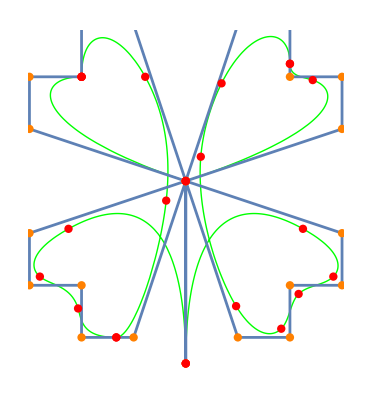

degree = 3  Number segments  = 24

knots = {0.,0.,0.,0.,0.1,0.2,0.3,0.35,0.35,0.375,0.4,0.45,0.45,0.45,0.5,0.5,0.5,0.575,0.6,0.6,0.675,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.,1.,1.}

-Graphics3D-

-Graphics3D-

-Graphics3D-

nalla_hw4.STL

-Graphics3D-

-Graphics3D-

```mathematica
(* This line makes MM read and write from your local folder, where this nb lives. *)
SetDirectory[ToFileName[
Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],
{1},FrontEnd`FileName]]];
(*Degree, domain intervals, and deboor points*)
(*24 polynomial segments*)
deg = 3;
di = 24;
dbpts = 26;
(*These points are later translated and scaled to fit [0,1] and [0,1]*)
dd={{0.00,-0.7},
{0.0,0.0},
{-0.6,-0.2},
{-0.6,-0.4},
{-0.4,-0.4},
{-0.4,-0.6},
{-0.2,-0.6},

{0.0,0.0},
{-0.2,0.6},
{-0.4,0.6},
{-0.4,0.4},
{-0.6,0.4},
{-0.6,0.2},

{0.0,0.0},
{0.6,0.2},
{0.6,0.4},
{0.4,0.4},
{0.4,0.6},
{0.2,0.6},

{0.0,0.0},
{0.2,-0.6},
{0.4,-0.6},
{0.4,-0.4},
{0.6,-0.4},
{0.6,-0.2},

{0.0,0.0},
{-0.00,-0.7}
};
dd=dd/. {x_,y_}->{(x+1)/2,(y+1)/2}
(*Knot of multiplicty 3 is 0.45 and 0.5, and knot of multiplicity 2 is 0.6 and 0.35. T *)
knot=Join[Table[0,{i,0,deg}],{0.1,0.2,0.3,0.35,0.35,0.375,0.4,0.45,0.45,0.45,0.5,0.5,0.5,0.575,0.6,0.6,0.675,0.7,0.75,0.8,0.85,0.9,0.95},{1,1,1,1}]//N;
numk = Length[knot];

(* evaluator *)
curve[t_]:=Sum[BSplineBasis[{deg,knot},i,t]*dd[[i+1]],{i,0,dbpts}];
jknots = Table[knot[[i]], {i,deg+1,numk - deg,1}];
jpts = Table[curve[knot[[i]]], {i,deg+1,numk - deg,1}];

(* Plot *)
cplot=ParametricPlot[curve[t],{t,knot[[deg+1]],knot[[numk-deg]]},PlotStyle->{Thick,Green}];
points=Graphics[{Orange,PointSize[0.015],Point[dd]}];
jpoints = Graphics[{Red,PointSize[0.015],Point[jpts]}];
ddplot=ListLinePlot[dd];

Show[{cplot,ddplot,points,jpoints},Axes-> False]

Print["degree = ",deg,"  Number segments  = ",di];
Print["knots = ",knot];

(*------------------------------------------------------------------------------------------------------------------------------------------------------------------*)

(* Here is one way to use the MM Bezier surface function. *)
(* create a surface defined by a set of control points *)
(*Bicubic bezier patch obtained from HW3 copying the control points*)
surfControlNet={{{-2,-2,1},{-1,-2,-1.5},{0,-2,-2},{1,-2,-1.5},{2,-2,0}},{{-2,-1,1.5},{-1,-1,0},{0,-1,-0.5},{1,-1,0},{2,-1,1.5}},{{-2,0,2},{-1,0,0.5},{0,0,0},{1,0,0.5},{2,0,2}},{{-2,1,1.5},{-1,1,0},{0,1,-0.5},{1,1,0},{2,1,1.5}},{{-2,2,0},{-1,2,-1.5},{0,2,-2},{1,2,-1.5},{2,2,0}}};
surf=BezierFunction[surfControlNet];
(* evaluate that surface at one (u,v) pair *)
surf[u,v];
(*Print[Table[surf[dd[[t]][[1]],dd[[t]][[2]]],{t,1,27}]];*)
surfPlot=ParametricPlot3D[surf[u,v],{u,0,1},{v,0,1},PlotStyle->{LightBlue}];
curvePlot=ParametricPlot3D[surf[curve[t][[1]],curve[t][[2]]],{t,0,1},PlotStyle->{Green}];
Show[surfPlot,curvePlot]

curvePlot=ParametricPlot3D[surf[curve[t][[1]],curve[t][[2]]],{t,0,1},PlotStyle->{Green,Tube[0.12]}]

curvePlot2=ParametricPlot3D[{surf[curve[t][[1]],curve[t][[2]]],(*original spline*)
surf[curve[t][[1]],curve[t][[2]]]+{1.5,1.5,0},
surf[curve[t][[1]],curve[t][[2]]]+{2.9,0.1,0}},
{t,0,1},PlotStyle->{{Green,Tube[0.12]},{Pink,Tube[0.12]},{LightBlue,Tube[0.12]}}]
(*Graphics3D[{{Green,Tube[Table[surf[curve[t][[1]],curve[t][[2]]],{t,0,1,0.01}],0.04]},{Pink,Tube[Table[surf[curve[t][[1]],curve[t][[2]]]+{1,0,0},{t,0,1,0.01}],0.04]},{LightBlue,Tube[Table[surf[curve[t][[1]],curve[t][[2]]]+{2,0,0},{t,0,1,0.01}],0.04]}}]*)


Export["nalla_hw4.STL", curvePlot2, "STL","BinaryFormat"->True]
Import["nalla_hw4.STL","Summary"]

(*The mesh does not render on this computer, will be emailing to teacher*)
shamrockMesh = Import["nalla_hw4.STL"]
shamrockMeshRegion = MeshRegion[shamrockMesh, PlotTheme->"Default"]
```